```mathematica
Quit[]
```

## Input

```mathematica
<<"/home/riccardo/Programs/FeynArts/FeynArts/FeynArts.m"
```

FeynArts 3.11 (25 Mar 2022)

by Hagen Eck, Sepp Kueblbeck, and Thomas Hahn

```mathematica
<<"/home/riccardo/Programs/FormCalc/FormCalc/FormCalc.m"
```

FormCalc 9.10 (30 Aug 2022)

by Thomas Hahn

```mathematica
Remove[q1]
Remove[q2]
<<"/home/riccardo/Programs/ABISS/ABISS.m"
```

+++++ ABISS` +++++
Version 1.0.0

Amplitudes Builder, Interference Solver and Simplifier

A link to the model file SMbgf_Anglerfish.mod has been added to the FeynArts directory

A link to the model file SMbgf_FARAMIR_general_backup.mod has been added to the FeynArts directory

A link to the model file SMbgf_FARAMIR_general+SM.mod has been added to the FeynArts directory

A link to the model file SMbgfQCD_Anglerfish.mod has been added to the FeynArts directory

A link to the model file SMbgf_TelescopeOctopus_backup.mod has been added to the FeynArts directory

```mathematica
SetPath[NotebookDirectory[]];
```

Define the process:

```mathematica
SetProcess[{V[20]}->{S[20]}];
```

Generate default Input files

```mathematica
GenerateInput[];
```

Input file /home/riccardo/Documents/Tesi/TestABISS/SE_Test/WX/input/kinematics.m already exist. It will NOT be overwritten.

Input file /home/riccardo/Documents/Tesi/TestABISS/SE_Test/WX/input/integral_families.m already exist. It will NOT be overwritten.

Import the input files (kinematics + integral families).

```mathematica
ImportInput[];
```

Imported input file /home/riccardo/Documents/Tesi/TestABISS/SE_Test/WX/input/integral_families.m.

Imported input file /home/riccardo/Documents/Tesi/TestABISS/SE_Test/WX/input/kinematics.m.

## Diagrams generation

Generate diagrams using feynarts (charged current drell-yan, one loop boxes and born).

```mathematica
SetOptions[InsertFields,  Model -> "SMbgf_Anglerfish", GenericModel ->"Lorentzbgf", InsertionLevel->{Particles}, Restrictions->{NoQuarkMixing}, ExcludeParticles-> {}];
```

```mathematica
process={V[30]}->{S[30]};
```

```mathematica
topologies1L=CreateTopologies[1,1-> 1,ExcludeTopologies->Tadpoles];
```

```mathematica
fields1L=InsertFields[topologies1L, process];
```

loading generic model file /home/riccardo/Programs/FeynArts/FeynArts/Models/Lorentzbgf.gen

> $GenericMixing is OFF

generic model {Lorentzbgf} initialized

loading classes model file /home/riccardo/Programs/FeynArts/FeynArts/Models/SMbgf_Anglerfish.mod

> 60 particles (incl. antiparticles) in 24 classes

> $CounterTerms are ON

> 689 vertices

> 334 counterterms of order 1

> 2 counterterms of order 2

classes model {SMbgf_Anglerfish} initialized

Excluding 24 field point(s) (incl. charge-conjugate ones)

inserting at level(s) {Particles}

> Top. 1: 0 Particles insertions

> Top. 2: 18 Particles insertions

Restoring 24 field point(s)

in total: 18 Particles insertions

```mathematica
amp1L=CreateFeynAmp[fields1L];
```

creating amplitudes at level(s) {Particles}

> Top. 1: 18 Particles amplitudes

in total: 18 Particles amplitudes

> Top. 1 ac/bd/cdcd.m, 0 diagrams

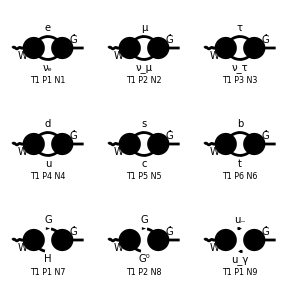

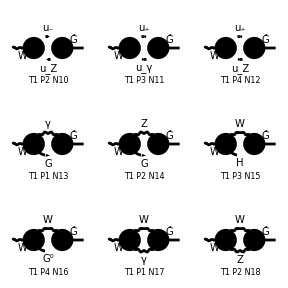

```mathematica
Paint[fields1L];
```

```mathematica
myAmp1L=ExtractAmplitude[amp1L];
```

```mathematica
SaveAmplitudes[myAmp1L,"OneLoopAmplitudes.m"];
```

Amplitudes saved in /home/riccardo/Documents/Tesi/TestABISS/SE_Test/WX/feynArts_amplitudes/OneLoopAmplitudes.m

## Projection and polarization vector

```mathematica
p[Lor1_]:=- I SP[p1,{Lor1}]/SP[p1,p1]
```

### Remove polarization vectors

```mathematica
removePolarizationVectors={PolarizationVector[V[30],p_,i_]->1}
```

{ep[V[30],p_,i_]→1}

## Interference

```mathematica
myAmp1LABISS=Map[AmpSquare[#,1]&,myAmp1L];
```

```mathematica
myAmp1LnoEP=myAmp1LABISS/.removePolarizationVectors;
```

```mathematica
myAmp1LProjection=Map[AmpSquare[#*p[Lor1],1]&,myAmp1LnoEP];
```

```mathematica
myAmp1LnoEP[[1]]
```

(ⅈ EL^2 gFll gWlN ME^2 KiraPropagator[q1,0] KiraPropagator[-p1+q1,ME] SP[q1,{Lor1}])/(8 π^4)

```mathematica
myAmp1LProjection[[1]]
```

(EL^2 gFll gWlN ME^2 KiraPropagator[q1,0] KiraPropagator[-p1+q1,ME] SP[p1,q1])/(8 π^4 psq)

```mathematica
SquareSimplifyAndSave[myAmp1LProjection,{1}]
```

Computed contribution 1-1.

Computed contribution 2-1.

Computed contribution 3-1.

Computed contribution 4-1.

Computed contribution 5-1.

Computed contribution 6-1.

Computed contribution 7-1.

Computed contribution 8-1.

Computed contribution 9-1.

Computed contribution 10-1.

Computed contribution 11-1.

Computed contribution 12-1.

Computed contribution 13-1.

Computed contribution 14-1.

Computed contribution 15-1.

Computed contribution 16-1.

Computed contribution 17-1.

Computed contribution 18-1.

## Shift

```mathematica
ImportInput[];
```

Imported input file /home/riccardo/Documents/Tesi/TestABISS/SE_Test/WX/input/integral_families.m.

Imported input file /home/riccardo/Documents/Tesi/TestABISS/SE_Test/WX/input/kinematics.m.

```mathematica
Do[
ShiftAndSave[i,j,False];
,{i,18},{j,1}]
```

Integral family {{E0, {ME}}} already recognised for /home/riccardo/Documents/Tesi/TestABISS/SE_Test/WX/interferences/Contribution_1_1.m.

Integral family {{E0, {MM}}} already recognised for /home/riccardo/Documents/Tesi/TestABISS/SE_Test/WX/interferences/Contribution_2_1.m.

Integral family {{E0, {ML}}} already recognised for /home/riccardo/Documents/Tesi/TestABISS/SE_Test/WX/interferences/Contribution_3_1.m.

Integral family {{C0, {MU, MD}}} already recognised for /home/riccardo/Documents/Tesi/TestABISS/SE_Test/WX/interferences/Contribution_4_1.m.

Integral family {{C0, {MC, MS}}} already recognised for /home/riccardo/Documents/Tesi/TestABISS/SE_Test/WX/interferences/Contribution_5_1.m.

Integral family {{C0, {MT, MB}}} already recognised for /home/riccardo/Documents/Tesi/TestABISS/SE_Test/WX/interferences/Contribution_6_1.m.

Integral family {{C0, {MH, MW}}} already recognised for /home/riccardo/Documents/Tesi/TestABISS/SE_Test/WX/interferences/Contribution_7_1.m.

Integral family {{C0, {MZ, MW}}} already recognised for /home/riccardo/Documents/Tesi/TestABISS/SE_Test/WX/interferences/Contribution_8_1.m.

Integral family {{E0, {MW}}} already recognised for /home/riccardo/Documents/Tesi/TestABISS/SE_Test/WX/interferences/Contribution_9_1.m.

Integral family {{C0, {MZ, MW}}} already recognised for /home/riccardo/Documents/Tesi/TestABISS/SE_Test/WX/interferences/Contribution_10_1.m.

Integral family {{E0, {MW}}} already recognised for /home/riccardo/Documents/Tesi/TestABISS/SE_Test/WX/interferences/Contribution_11_1.m.

Integral family {{C0, {MZ, MW}}} already recognised for /home/riccardo/Documents/Tesi/TestABISS/SE_Test/WX/interferences/Contribution_12_1.m.

Integral family {{D0, {MW}}} already recognised for /home/riccardo/Documents/Tesi/TestABISS/SE_Test/WX/interferences/Contribution_13_1.m.

Integral family {{C0, {MW, MZ}}} already recognised for /home/riccardo/Documents/Tesi/TestABISS/SE_Test/WX/interferences/Contribution_14_1.m.

Integral family {{C0, {MH, MW}}} already recognised for /home/riccardo/Documents/Tesi/TestABISS/SE_Test/WX/interferences/Contribution_15_1.m.

Integral family {{C0, {MZ, MW}}} already recognised for /home/riccardo/Documents/Tesi/TestABISS/SE_Test/WX/interferences/Contribution_16_1.m.

Integral family {{E0, {MW}}} already recognised for /home/riccardo/Documents/Tesi/TestABISS/SE_Test/WX/interferences/Contribution_17_1.m.

Integral family {{C0, {MZ, MW}}} already recognised for /home/riccardo/Documents/Tesi/TestABISS/SE_Test/WX/interferences/Contribution_18_1.m.

## KiraInput

```mathematica
Do[
GenerateAndSaveKiraInput[i,j];
,{i,18},{j,1}]
```

Overwritten file /home/riccardo/Documents/Tesi/TestABISS/SE_Test/WX/kira_input/Contribution_1_1.m.

Overwritten file /home/riccardo/Documents/Tesi/TestABISS/SE_Test/WX/kira_input/Contribution_2_1.m.

Overwritten file /home/riccardo/Documents/Tesi/TestABISS/SE_Test/WX/kira_input/Contribution_3_1.m.

Overwritten file /home/riccardo/Documents/Tesi/TestABISS/SE_Test/WX/kira_input/Contribution_4_1.m.

Overwritten file /home/riccardo/Documents/Tesi/TestABISS/SE_Test/WX/kira_input/Contribution_5_1.m.

Overwritten file /home/riccardo/Documents/Tesi/TestABISS/SE_Test/WX/kira_input/Contribution_6_1.m.

Overwritten file /home/riccardo/Documents/Tesi/TestABISS/SE_Test/WX/kira_input/Contribution_7_1.m.

Overwritten file /home/riccardo/Documents/Tesi/TestABISS/SE_Test/WX/kira_input/Contribution_8_1.m.

Overwritten file /home/riccardo/Documents/Tesi/TestABISS/SE_Test/WX/kira_input/Contribution_9_1.m.

Overwritten file /home/riccardo/Documents/Tesi/TestABISS/SE_Test/WX/kira_input/Contribution_10_1.m.

Overwritten file /home/riccardo/Documents/Tesi/TestABISS/SE_Test/WX/kira_input/Contribution_11_1.m.

Overwritten file /home/riccardo/Documents/Tesi/TestABISS/SE_Test/WX/kira_input/Contribution_12_1.m.

Overwritten file /home/riccardo/Documents/Tesi/TestABISS/SE_Test/WX/kira_input/Contribution_13_1.m.

```mathematica
PrintScalarIntegrals[]
```

{userIntegral[E0,{ME},1,1],userIntegral[E0,{MM},1,1],userIntegral[E0,{ML},1,1],userIntegral[C0,{MU,MD},1,1],userIntegral[C0,{MC,MS},1,1],userIntegral[C0,{MT,MB},1,1],userIntegral[C0,{MH,MW},1,1],userIntegral[C0,{MZ,MW},1,1],userIntegral[E0,{MW},1,1],userIntegral[D0,{MW},1,1],userIntegral[C0,{MW,MZ},1,1]}

```mathematica
SaveScalarIntegrals["scalar_integrals"];
```

```mathematica
ExportScalarIntegrals["kira_scalar_integrals.dat"];
```

## Apply Kira sub;

```mathematica
ImportScalarIntegrals["scalar_integrals"];
```

```mathematica
ClearRules[]
```

{}

```mathematica
ImportRules[NotebookDirectory[]<>"kira_myintegrals.m"]
```

```mathematica
PrintRules[]
```

{userIntegral[A0,{0},1,0]→0,userIntegral[E0,{m1},1,1]→userIntegral[D0,{m1},1,1]}

```mathematica
PrintScalarIntegrals[]
```

{userIntegral[E0,{ME},1,1],userIntegral[E0,{MM},1,1],userIntegral[E0,{ML},1,1],userIntegral[C0,{MU,MD},1,1],userIntegral[C0,{MC,MS},1,1],userIntegral[C0,{MT,MB},1,1],userIntegral[C0,{MH,MW},1,1],userIntegral[C0,{MZ,MW},1,1],userIntegral[E0,{MW},1,1],userIntegral[D0,{MW},1,1],userIntegral[C0,{MW,MZ},1,1]}

```mathematica
DetermineMasterIntegrals[]
```

```mathematica
PrintMasterIntegrals[]
```

{userIntegral[D0,{ME},1,1],userIntegral[D0,{MM},1,1],userIntegral[D0,{ML},1,1],userIntegral[C0,{MU,MD},1,1],userIntegral[C0,{MC,MS},1,1],userIntegral[C0,{MT,MB},1,1],userIntegral[C0,{MH,MW},1,1],userIntegral[C0,{MZ,MW},1,1],userIntegral[D0,{MW},1,1],userIntegral[C0,{MW,MZ},1,1]}

```mathematica
Do[
SaveResult[i,j];
,{i,13},{j,1}]
```

## Ward Identity Test

### Total coefficients

```mathematica
diagramCoefficients= {};
Do[diagramCoefficients=Append[diagramCoefficients,<<(NotebookDirectory[]<>"coefficients/Coefficients_"<>ToString[i]<>"_1.m")],{i,13}]
```

```mathematica
diagramCoefficients
```

{{(EL^2 gFll gWlN ME^2 SP[p1,q1])/(8 π^4 psq),0,0,0,0,0,0,0,0,0},{0,(EL^2 gFll gWlN MM^2 SP[p1,q1])/(8 π^4 psq),0,0,0,0,0,0,0,0},{0,0,(EL^2 gFll gWlN ML^2 SP[p1,q1])/(8 π^4 psq),0,0,0,0,0,0,0},{0,0,0,(3 EL^2 gFud gWdu MU^2 CKM[1,1] CKMC[1,1])/(8 π^4)+(3 EL^2 gFud gWdu MD^2 CKM[1,1] CKMC[1,1] SP[p1,q1])/(8 π^4 psq)-(3 EL^2 gFud gWdu MU^2 CKM[1,1] CKMC[1,1] SP[p1,q1])/(8 π^4 psq),0,0,0,0,0,0},{0,0,0,0,(3 EL^2 gFud gWdu MC^2 CKM[2,2] CKMC[2,2])/(8 π^4)-(3 EL^2 gFud gWdu MC^2 CKM[2,2] CKMC[2,2] SP[p1,q1])/(8 π^4 psq)+(3 EL^2 gFud gWdu MS^2 CKM[2,2] CKMC[2,2] SP[p1,q1])/(8 π^4 psq),0,0,0,0,0},{0,0,0,0,0,(3 EL^2 gFud gWdu MT^2 CKM[3,3] CKMC[3,3])/(8 π^4)+(3 EL^2 gFud gWdu MB^2 CKM[3,3] CKMC[3,3] SP[p1,q1])/(8 π^4 psq)-(3 EL^2 gFud gWdu MT^2 CKM[3,3] CKMC[3,3] SP[p1,q1])/(8 π^4 psq),0,0,0,0},{0,0,0,0,0,0,(EL^2 gHFF gHFW MH^2)/(16 π^4)-(EL^2 gHFF gHFW MW^2)/(16 π^4)-(EL^2 gHFF gHFW MH^2 SP[p1,q1])/(8 π^4 psq)+(EL^2 gHFF gHFW MW^2 SP[p1,q1])/(8 π^4 psq),0,0,0},{0,0,0,0,0,0,0,-(EL^2 gXFF gXFW)/(16 π^4)+(EL^2 gXFF gXFW SP[p1,q1])/(8 π^4 psq),0,0},{0,0,0,0,0,0,0,0,-(EL^2 gFgagm ggagmW)/(16 π^4)+(EL^2 gFgagm ggagmW SP[p1,q1])/(8 π^4 psq),0},{0,0,0,0,0,0,0,(EL^2 gFgzgm ggzgmW SW)/(16 π^4)-(EL^2 gFgzgm ggzgmW SW SP[p1,q1])/(8 π^4 psq),0,0},{0,0,0,0,0,0,0,0,-(EL^2 gFgagp ggagpW)/(16 π^4)+(EL^2 gFgagp ggagpW SP[p1,q1])/(8 π^4 psq),0},{0,0,0,0,0,0,0,(EL^2 gFgzgp ggzgpW SW)/(16 π^4)-(EL^2 gFgzgp ggzgpW SW SP[p1,q1])/(8 π^4 psq),0,0},{0,0,0,0,0,0,0,0,(EL^2 gFAW gFFA)/(4 π^4),0}}

```mathematica
coefficients=Plus@@diagramCoefficients
```

{(EL^2 gFll gWlN ME^2 SP[p1,q1])/(8 π^4 psq),(EL^2 gFll gWlN MM^2 SP[p1,q1])/(8 π^4 psq),(EL^2 gFll gWlN ML^2 SP[p1,q1])/(8 π^4 psq),(3 EL^2 gFud gWdu MU^2 CKM[1,1] CKMC[1,1])/(8 π^4)+(3 EL^2 gFud gWdu MD^2 CKM[1,1] CKMC[1,1] SP[p1,q1])/(8 π^4 psq)-(3 EL^2 gFud gWdu MU^2 CKM[1,1] CKMC[1,1] SP[p1,q1])/(8 π^4 psq),(3 EL^2 gFud gWdu MC^2 CKM[2,2] CKMC[2,2])/(8 π^4)-(3 EL^2 gFud gWdu MC^2 CKM[2,2] CKMC[2,2] SP[p1,q1])/(8 π^4 psq)+(3 EL^2 gFud gWdu MS^2 CKM[2,2] CKMC[2,2] SP[p1,q1])/(8 π^4 psq),(3 EL^2 gFud gWdu MT^2 CKM[3,3] CKMC[3,3])/(8 π^4)+(3 EL^2 gFud gWdu MB^2 CKM[3,3] CKMC[3,3] SP[p1,q1])/(8 π^4 psq)-(3 EL^2 gFud gWdu MT^2 CKM[3,3] CKMC[3,3] SP[p1,q1])/(8 π^4 psq),(EL^2 gHFF gHFW MH^2)/(16 π^4)-(EL^2 gHFF gHFW MW^2)/(16 π^4)-(EL^2 gHFF gHFW MH^2 SP[p1,q1])/(8 π^4 psq)+(EL^2 gHFF gHFW MW^2 SP[p1,q1])/(8 π^4 psq),-(EL^2 gXFF gXFW)/(16 π^4)+(EL^2 gFgzgm ggzgmW SW)/(16 π^4)+(EL^2 gFgzgp ggzgpW SW)/(16 π^4)+(EL^2 gXFF gXFW SP[p1,q1])/(8 π^4 psq)-(EL^2 gFgzgm ggzgmW SW SP[p1,q1])/(8 π^4 psq)-(EL^2 gFgzgp ggzgpW SW SP[p1,q1])/(8 π^4 psq),(EL^2 gFAW gFFA)/(4 π^4)-(EL^2 gFgagm ggagmW)/(16 π^4)-(EL^2 gFgagp ggagpW)/(16 π^4)+(EL^2 gFgagm ggagmW SP[p1,q1])/(8 π^4 psq)+(EL^2 gFgagp ggagpW SP[p1,q1])/(8 π^4 psq),0}

### Lagrangian parameter replace

```mathematica
<<(NotebookDirectory[]<>"smparameters.m")
parameterReplace=smparameters
```

{gZlL→(-1/2+SW^2)/(CW SW),gZlR→SW/CW,gZNL→1/(2 CW SW),gZuL→(1/2-(2 SW^2)/3)/(CW SW),gZuR→-(2 SW)/(3 CW),gZdL→(-1/2+SW^2/3)/(CW SW),gZdR→SW/(3 CW),gAl→1,gAu→-2/3,gAd→1/3,gWNl→1/(√2 SW),gWlN→1/(√2 SW),gWud→1/(√2 SW),gWdu→1/(√2 SW),gWWZ→CW/SW,gWWA→1,gWWWW→1/SW^2,gWWZZ→-CW^2/SW^2,gWWAZ→CW/SW,gWWAA→-1,gHHHH→-3/(4 MW^2 SW^2),gXXXX→-3/(4 MW^2 SW^2),gHHXX→1/(2 SW^2),gHHFF→1/(2 SW^2),gXXFF→1/(2 SW^2),gFFFF→1/(2 SW^2),gHXFF→1/(4 CW^2),gHHH→-3/(2 MW SW),gHXX→-1/(2 MW SW),gHFF→-1/(2 MW SW),gXFF→(MW SW)/(2 CW^2),gHHZZ→1/(2 CW^2 SW^2),gXXZZ→1/(2 CW^2 SW^2),gHHWW→1/(2 SW^2),gXXWW→1/(2 SW^2),gFFWW→1/(2 SW^2),gFFAA→2,gFFAZ→(-CW^2+SW^2)/(CW SW),gFFZZ→((-CW^2+SW^2)^2)/(2 CW^2 SW^2),gHFAW→-1/(2 SW),gHFZW→-1/(2 CW),gXFAW→1/(2 SW),gHFZW→-1/(2 CW),gXFZW→1/(2 CW),gHXWW→1/(2 SW^2),gHXZ→1/(2 CW SW),gFFA→1,gFFZ→(CW^2-SW^2)/(2 CW SW),gHFW→1/(2 SW),gXFW→1/(2 SW),gHZZ→MW/(CW^2 SW),gHWW→MW/SW,gXWW→MW/SW,gFAW→-MW,gFZW→MW/CW,gHll→-1/(2 MW SW),gHuu→-1/(2 MW SW),gHdd→-1/(2 MW SW),gXll→1/(2 MW SW),gXuu→1/(2 MW SW),gXdd→1/(2 MW SW),gFll→1/(√2 MW SW),gFud→1/(√2 MW SW),gFdu→1/(√2 MW SW),ggpgpA→1,ggmgmA→1,ggpgpZ→CW/SW,ggmgmZ→CW/SW,ggzgpW→CW/SW,ggzgmW→CW/SW,ggagpW→1,ggagmW→1,gHgzgz→-MW/(CW^2 SW),gHgpgp→-MW/SW,gHgmgm→-MW/SW,gXgpgp→MW/(2 SW),gXgmgm→MW/(2 SW),gFgzgp→MW/CW,gFgzgm→MW/CW,gFgagm→MW,gFgagp→MW,ggpgpAA→1,ggmgmAA→1,ggpgpAZ→-CW/SW,ggmgmAZ→-CW/SW,ggpgpZZ→CW^2/SW^2,ggmgmZZ→CW^2/SW^2,ggagpAW→-1,ggagmAW→-1,ggagpZW→CW/SW,ggagmZW→CW/SW,ggzgpAW→CW/SW,ggzgmAW→CW/SW,ggzgpZW→-CW^2/SW^2,ggzgmZW→-CW^2/SW^2,ggagaWW→1,ggagzWW→-CW/SW,ggzgzWW→CW^2/SW^2,ggpgpWW→1/SW^2,ggmgmWW→1/SW^2,ggpgmWW→-1/SW^2,gHHgzgz→-1/(2 CW^2 SW^2),gHHgpgp→-1/(2 SW^2),gHHgmgm→-1/(2 SW^2),gXXgzgz→-1/(2 CW^2 SW^2),gXXgpgp→-1/(2 SW^2),gXXgmgm→-1/(2 SW^2),gFFgaga→-1,gFFgzgz→((CW^2-SW^2)^2)/(2 CW^2 SW^2),gFFgpgp→-1/(2 SW^2),gFFgmgm→-1/(2 SW^2),gFFgagz→(CW^2-SW^2)/(CW SW),gHXgpgp→1/(4 SW^2),gHXgmgm→1/(4 SW^2),gHFgagp→1/(2 SW),gHFgagm→1/(2 SW),gHFgzgp→1/(2 CW),gHFgzgm→1/(2 CW),gXFgagp→1/(2 SW),gXFgagm→1/(2 SW),gXFgzgp→1/(2 CW),gXFgzgm→1/(2 CW)}

```mathematica
coefficients/.parameterReplace//Simplify
```

{(EL^2 ME^2 SP[p1,q1])/(16 MW π^4 psq SW^2),(EL^2 MM^2 SP[p1,q1])/(16 MW π^4 psq SW^2),(EL^2 ML^2 SP[p1,q1])/(16 MW π^4 psq SW^2),(3 EL^2 CKM[1,1] CKMC[1,1] (MU^2 psq+(MD^2-MU^2) SP[p1,q1]))/(16 MW π^4 psq SW^2),(3 EL^2 CKM[2,2] CKMC[2,2] (MC^2 psq+(-MC^2+MS^2) SP[p1,q1]))/(16 MW π^4 psq SW^2),(3 EL^2 CKM[3,3] CKMC[3,3] (MT^2 psq+(MB^2-MT^2) SP[p1,q1]))/(16 MW π^4 psq SW^2),(EL^2 (-MH^2+MW^2) (psq-2 SP[p1,q1]))/(64 MW π^4 psq SW^2),((-1+8 CW^2) EL^2 MW (psq-2 SP[p1,q1]))/(64 CW^2 π^4 psq),-(EL^2 MW (3 psq-2 SP[p1,q1]))/(8 π^4 psq),0}

```mathematica
cfinal=(I MZ coefficients/.parameterReplace)//Simplify
```

{(ⅈ EL^2 ME^2 MZ SP[p1,q1])/(16 MW π^4 psq SW^2),(ⅈ EL^2 MM^2 MZ SP[p1,q1])/(16 MW π^4 psq SW^2),(ⅈ EL^2 ML^2 MZ SP[p1,q1])/(16 MW π^4 psq SW^2),(3 ⅈ EL^2 MZ CKM[1,1] CKMC[1,1] (MU^2 psq+(MD^2-MU^2) SP[p1,q1]))/(16 MW π^4 psq SW^2),(3 ⅈ EL^2 MZ CKM[2,2] CKMC[2,2] (MC^2 psq+(-MC^2+MS^2) SP[p1,q1]))/(16 MW π^4 psq SW^2),(3 ⅈ EL^2 MZ CKM[3,3] CKMC[3,3] (MT^2 psq+(MB^2-MT^2) SP[p1,q1]))/(16 MW π^4 psq SW^2),(ⅈ EL^2 (-MH^2+MW^2) MZ (psq-2 SP[p1,q1]))/(64 MW π^4 psq SW^2),(ⅈ (-1+8 CW^2) EL^2 MW MZ (psq-2 SP[p1,q1]))/(64 CW^2 π^4 psq),-(ⅈ EL^2 MW MZ (3 psq-2 SP[p1,q1]))/(8 π^4 psq),0}

```mathematica
c=cfinal/.MW->MZ CW //Simplify
```

{(ⅈ EL^2 ME^2 SP[p1,q1])/(16 CW π^4 psq SW^2),(ⅈ EL^2 MM^2 SP[p1,q1])/(16 CW π^4 psq SW^2),(ⅈ EL^2 ML^2 SP[p1,q1])/(16 CW π^4 psq SW^2),(3 ⅈ EL^2 CKM[1,1] CKMC[1,1] (MU^2 psq+(MD^2-MU^2) SP[p1,q1]))/(16 CW π^4 psq SW^2),(3 ⅈ EL^2 CKM[2,2] CKMC[2,2] (MC^2 psq+(-MC^2+MS^2) SP[p1,q1]))/(16 CW π^4 psq SW^2),(3 ⅈ EL^2 CKM[3,3] CKMC[3,3] (MT^2 psq+(MB^2-MT^2) SP[p1,q1]))/(16 CW π^4 psq SW^2),(ⅈ EL^2 (-MH^2+CW^2 MZ^2) (psq-2 SP[p1,q1]))/(64 CW π^4 psq SW^2),(ⅈ (-1+8 CW^2) EL^2 MZ^2 (psq-2 SP[p1,q1]))/(64 CW π^4 psq),-(ⅈ CW EL^2 MZ^2 (3 psq-2 SP[p1,q1]))/(8 π^4 psq),0}

```mathematica
PrintMasterIntegrals[]
```

{userIntegral[D0,{ME},1,1],userIntegral[D0,{MM},1,1],userIntegral[D0,{ML},1,1],userIntegral[C0,{MU,MD},1,1],userIntegral[C0,{MC,MS},1,1],userIntegral[C0,{MT,MB},1,1],userIntegral[C0,{MH,MW},1,1],userIntegral[C0,{MZ,MW},1,1],userIntegral[D0,{MW},1,1],userIntegral[C0,{MW,MZ},1,1]}

```mathematica
m=<<(NotebookDirectory[]<>"coefficients/Masters.m");
```

```mathematica
Plus@@(c m)
```

(3 ⅈ EL^2 CKM[2,2] CKMC[2,2] (MC^2 psq+(-MC^2+MS^2) SP[p1,q1]) userIntegral[C0,{MC,MS},1,1])/(16 CW π^4 psq SW^2)+(ⅈ EL^2 (-MH^2+CW^2 MZ^2) (psq-2 SP[p1,q1]) userIntegral[C0,{MH,MW},1,1])/(64 CW π^4 psq SW^2)+(3 ⅈ EL^2 CKM[3,3] CKMC[3,3] (MT^2 psq+(MB^2-MT^2) SP[p1,q1]) userIntegral[C0,{MT,MB},1,1])/(16 CW π^4 psq SW^2)+(3 ⅈ EL^2 CKM[1,1] CKMC[1,1] (MU^2 psq+(MD^2-MU^2) SP[p1,q1]) userIntegral[C0,{MU,MD},1,1])/(16 CW π^4 psq SW^2)+(ⅈ (-1+8 CW^2) EL^2 MZ^2 (psq-2 SP[p1,q1]) userIntegral[C0,{MZ,MW},1,1])/(64 CW π^4 psq)+(ⅈ EL^2 ME^2 SP[p1,q1] userIntegral[D0,{ME},1,1])/(16 CW π^4 psq SW^2)+(ⅈ EL^2 ML^2 SP[p1,q1] userIntegral[D0,{ML},1,1])/(16 CW π^4 psq SW^2)+(ⅈ EL^2 MM^2 SP[p1,q1] userIntegral[D0,{MM},1,1])/(16 CW π^4 psq SW^2)-(ⅈ CW EL^2 MZ^2 (3 psq-2 SP[p1,q1]) userIntegral[D0,{MW},1,1])/(8 π^4 psq)